```mathematica
(* This does the stack of triangular Plaquettes --- reproducing David Berensteins notebook

The full form is not yet implemented 

H = \sum_s[g^2 E(s)^2_s + 1/g^2 B(s)^2_+ alpha Link (B(s)_extra)^2 ]
 
All term sare positve: With Wilson Plaq
B^2(s) = Tr[1 - U_p - U^\dag_p](s) 
 (B(s)_etra)^2 = \sum_s Tr[2 - U(s)U^\dag(s+1) - U(s+1)U^\dag(s)] 

For U(1) Qubits Links:   U      --> sigma^+ = (sigma^x + i sigma^y)/2
                        U^\dag --> sigma^- = (sigma^x - i sigma^y)/2

E(s) = sigma^z(s) +  sigma^z(s+1)

Conventions for Qubit kernel construction *)

Sigma[0] = IdentityMatrix[2]
Sigma[1] = {{0, 1}, {1, 0}}
Sigma[2] = {{0, -I}, {I, 0}}
Sigma[3] = {{1, 0}, {0, -1}}
SigmaP= (Sigma[1]+ I*Sigma[2])/2
SigmaM= (Sigma[1]- I*Sigma[2])/2
```

{{1,0},{0,1}}

{{0,1},{1,0}}

{{0,-ⅈ},{ⅈ,0}}

{{1,0},{0,-1}}

{{0,1},{0,0}}

{{0,0},{1,0}}

```mathematica
F
```

F

```mathematica
(* Start one layer *)
(* Kronecker builds multi-Qubit tensor:  Left most matrix has fast  -- low bit -- convention 
Lables of N = nQubit tensor should be   sigma_{N} x sigma_{N-1} x  ... x  sigma_{0}   *)
(* Plaquette term *)
```

```mathematica
(* Insert InsertSigma[ a = sigma_type , j = postion = 0,1,..., nQubit-1] *)
```

```mathematica
InsertSigma[ a_, j_, nQubit_]:=KroneckerProduct[IdentityMatrix[2^(nQubit-j -1)], Sigma[a], IdentityMatrix[2^j]]
MatrixForm[InsertSigma[3, 1, 2]]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
(* Plaquetts  at s = layer number *)
```

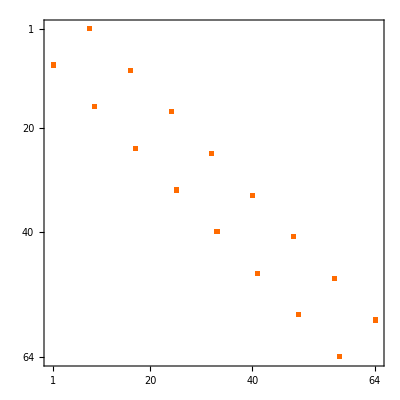

```mathematica
PlaqSingle[s_, nQubit_] := KroneckerProduct[ IdentityMatrix[2^(3*(s-1))],SigmaP, SigmaP, SigmaP,IdentityMatrix[2^(nQubit-3*s)]]+KroneckerProduct[IdentityMatrix[2^(3*(s-1))], SigmaM, SigmaM, SigmaM, IdentityMatrix[2^(nQubit-3*s)]]
MatrixPlot[PlaqSingle[2,6]]
```

```mathematica
Plaq[nQubit_] := Sum[PlaqSingle[s, nQubit],{s,1,nQubit/3}]
```

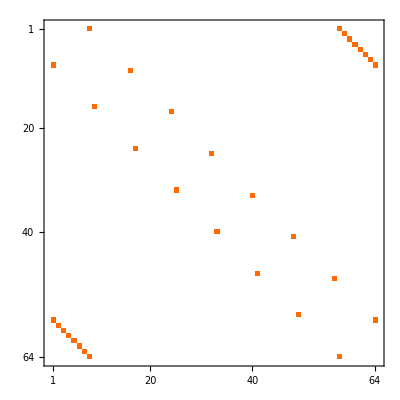

```mathematica
MatrixPlot[Plaq[6]]
```

```mathematica
(* Electric term between layers for two layer of triangular plaquette sigmaz_{j+3) x sigmaz(j) note + convention on Qubit operators *)
 
El[nQubit_] := Sum[InsertSigma[3,Mod[j+3,nQubit], nQubit].InsertSigma[3, Mod[j,nQubit], nQubit],{j,0,nQubit-1}]
```

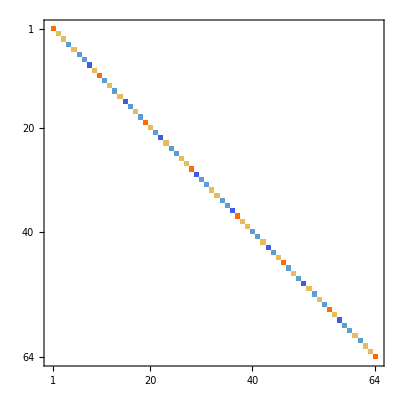

```mathematica
MatrixPlot[El[6]]
```

```mathematica
(* XX + YY chain *)
```

```mathematica
Coup[nQubit_] :=Sum[InsertSigma[1,Mod[j+3,nQubit], nQubit].InsertSigma[1, Mod[j,nQubit], nQubit],{j,0,nQubit-1}]+
Sum[InsertSigma[2,Mod[j+3,nQubit], nQubit].InsertSigma[2, Mod[j,nQubit], nQubit],{j,0,nQubit-1}]
```

```mathematica
(* Sign are choosen to be "right" of Hamilton *)
```

```mathematica
H[a_, b_, c_, nQubit_]:=a*El[nQubit]-  b*Coup[nQubit] - c*Plaq[nQubit]
```

```mathematica
MatrixPlot[H[-1, 1, 1, 9]]
```

-Graphics-

```mathematica
Eigs[a_, b_, c_, nQubit_, k_] := Sort[Eigenvalues[H[a, b, c, nQubit], k], Less]
```

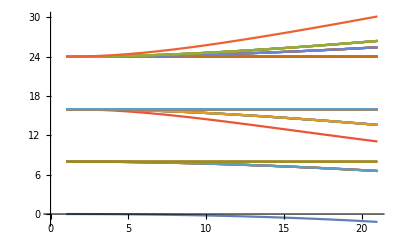

```mathematica
ListPlot[Transpose[Table[Eigs[1, 1, c, 6, 2^6] +18, {c, 0, 5, 0.25}]], Joined->True]
```

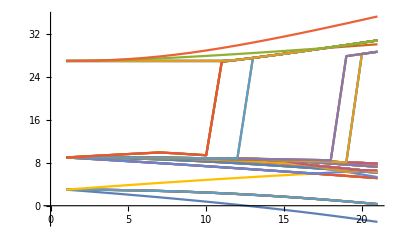

```mathematica
ListPlot[Transpose[Table[Eigs[1, 1, c, 9, 2^6] +18, {c, 0, 5, 0.25}]], Joined->True]
```

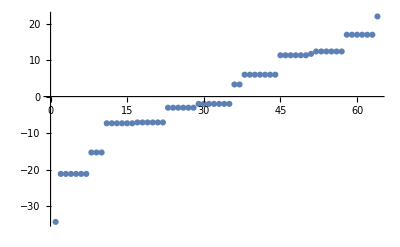

```mathematica
ListPlot[Eigs[1, 2.33, 3.88,6 , 2^6]]
```

```mathematica
Eigs[1, 2.33, 3.88,6 , 2^6]//N
```

{-34.3446,-21.1906,-21.1906,-21.1906,-21.1906,-21.1906,-21.1906,-15.32,-15.32,-15.32,-7.32,-7.32,-7.32,-7.32,-7.32,-7.32,-7.08212,-7.08212,-7.08212,-7.08212,-7.08212,-7.08212,-3.04779,-3.04779,-3.04779,-3.04779,-3.04779,-3.04779,-2.00701,-2.,-2.,-2.,-2.,-2.,-2.,3.32,3.32,6.,6.,6.,6.,6.,6.,6.,11.32,11.32,11.32,11.32,11.32,11.32,11.7116,12.3678,12.3678,12.3678,12.3678,12.3678,12.3678,16.9527,16.9527,16.9527,16.9527,16.9527,16.9527,21.96}

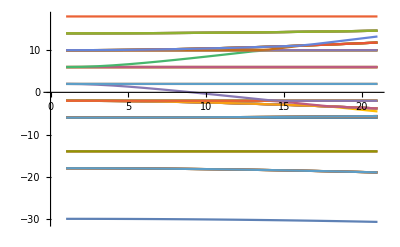

```mathematica
ListPlot[Transpose[Table[Eigs[1, 2, c, 6, 2^6], {c, 0,5, 0.25}]], Joined->True]
```

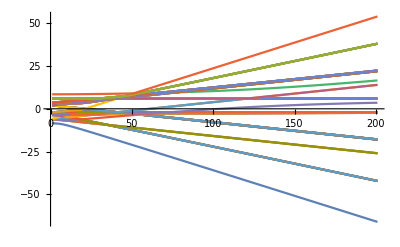

```mathematica
ListPlot[Transpose[Table[Eigs[1, b, 3, 6, 2^6], {b, 0, 5, 0.025}]], Joined->True]
```

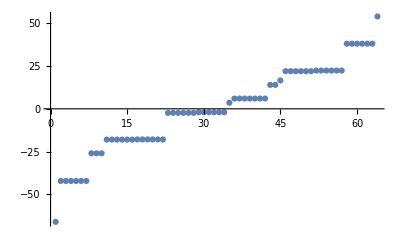

```mathematica
ListPlot[Eigs[1, 5, 3, 6, 2^6]]
```

```mathematica
Eigs[1, 5, 3, 6, 2^6]//N
```

{-66.1254,-42.1865,-42.1865,-42.1865,-42.1865,-42.1865,-42.1865,-26.,-26.,-26.,-18.,-18.,-18.,-18.,-18.,-18.,-17.8938,-17.8938,-17.8938,-17.8938,-17.8938,-17.8938,-2.36932,-2.36932,-2.36932,-2.36932,-2.36932,-2.36932,-2.,-2.,-2.,-2.,-2.,-2.,3.54653,6.,6.,6.,6.,6.,6.,6.,14.,14.,16.5788,22.,22.,22.,22.,22.,22.,22.3693,22.3693,22.3693,22.3693,22.3693,22.3693,38.0803,38.0803,38.0803,38.0803,38.0803,38.0803,54.}

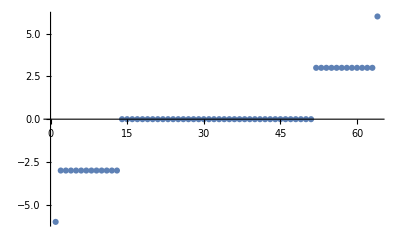

```mathematica
ListPlot[Eigs[0, 0, 3, 6, 2^6]]
```

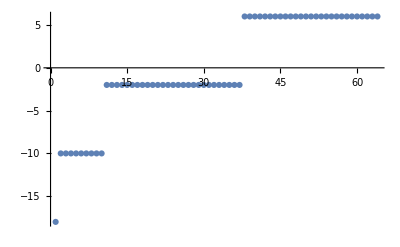

```mathematica
ListPlot[Eigs[1, 1, 0, 6, 2^6]]
```